Constructing RMT theoretical prediction...

Starting CUE simulation for 2000 matrices of size N=4...

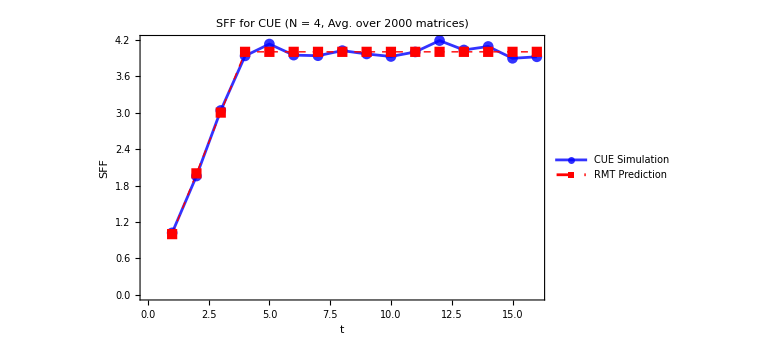

```mathematica
ClearAll["Global`*"];

(*Mathematica Code to Simulate the Spectral Form Factor (SFF) for the Circular Unitary Ensemble (CUE)*)

(***1. Parameters***)

(*Matrix dimension (N)*)
n=4;

(*Number of random matrices to average over*)
numMatrices=2000;

(*Maximum time (integer) to calculate SFF*)
(*We'll go to 2*n to see both the ramp and the plateau*)
tMax=4*n;


(***2. RMT Theoretical Prediction***)

Print["Constructing RMT theoretical prediction..."];

(*RMT prediction for SFF K(t)=<|Tr(U^t)|^2>For 1<=t<n,K(t)=t (the "ramp") For t>=n,K(t)=n (the "plateau")*)
rmtSFF[t_Integer,n_Integer]:=Min[t,n]

(*Create a list of {t,K(t)} pairs for plotting*)
tValues=Range[1,tMax];
rmtData=Table[{t,rmtSFF[t,n]},{t,tValues}];


(***3. Numerical CUE Simulation***)

Print["Starting CUE simulation for "<>ToString[numMatrices]<>" matrices of size N="<>ToString[n]<>"..."];

(*We need the eigenphases {θ_j} for each matrix.Tr(U^t)=Sum[Exp[I*θ_j*t]]*)

(*Generate all sets of eigenphases first*)
(*This is the most computationally intensive step*)
phaseSets=
Table[
(*Generate one CUE matrix*)
u=RandomVariate[CircularUnitaryMatrixDistribution[n]];
(*Get the arguments (phases) of its eigenvalues*)
Arg[Eigenvalues[u]],

{numMatrices}
];

(*Helper function to calculate SFF|Tr(U^t)|^2 for a*single*matrix*)
sffInstance[phases_List,t_Integer]:=Abs[Total[Exp[I*phases*t]]]^2

(*Calculate SFF for all matrices and all times.sffAll will be a 2D table:{numMatrices,tMax}*)
sffAll=Table[sffInstance[phaseSets[[k]],t],{k,1,numMatrices},(*Loop over matrices*){t,tValues}         (*Loop over time*)];

(*Average over all the matrix realizations (the first dimension) to get the final simulated SFF.*)
sffSimulated=Mean[sffAll];

(*Combine with tValues for plotting*)
simulatedData=Transpose[{tValues,sffSimulated}];

ListPlot[{simulatedData,rmtData},
(*Plot Styling*)
Joined->True,
PlotMarkers->Automatic,
PlotStyle->{
{Blue,Opacity[0.8],PointSize[0.01]},(*Simulation data*)
{Red,Thick,Dashed}                                           (*RMT prediction*)
},
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t","SFF"},

(*Labels and Legends*)
PlotLegends->{"CUE Simulation","RMT Prediction"},
LabelStyle->Directive[Black,FontSize->25],

AxesLabel->{"Time t (integer)","Spectral Form Factor K(t)"},PlotLabel->Style["SFF for CUE\n(N = "<>ToString[n]<>", Avg. over "<>ToString[numMatrices]<>" matrices)",Black,FontSize->25],
(*GridLines->Automatic,*)
ImageSize->Large]
```

Construyendo la prediccion teorica de RMT (COE)...

Iniciando simulacion de COE para 5000 matrices de dimension N=10...

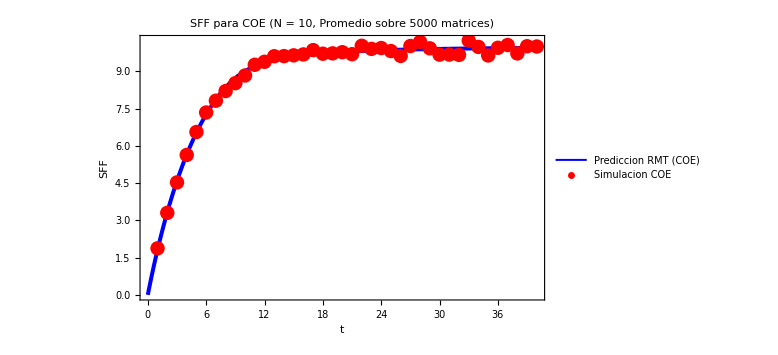

```mathematica
ClearAll["Global`*"];

(*Codigo de Mathematica para simular el Factor de Forma Espectral (SFF) para el Ensamblaje Circular Ortogonal (COE)*)

(***1. Parametros***)

(*Dimension de la matriz (N)*)
n=10;

(*Numero de matrices aleatorias para promediar*)
numMatrices=5000;

(*Tiempo maximo (entero) para calcular el SFF*)
(*Iremos a 4*n para ver tanto la rampa como el plateau*)
tMax=4*n;

(***2. Prediccion Teorica de RMT (para COE)***)

Print["Construyendo la prediccion teorica de RMT (COE)..."];

(*Prediccion de RMT para el SFF K(t)=<|Tr(O^t)|^2>para COE (beta=1) Para 1<=t<n,K(t)=2t-1 (la "rampa") Para t>=n,K(t)=2n-1 (el "plateau")*)
rmtSFF[τ_,n_Integer]:=With[{t=τ/n},n*If[t<1,2*t-t*Log[1+2*t],2-t*Log[(2*t+1)/(2*t-1)]]]

(*Crear una lista de pares {t,K(t)} para graficar*)
tValues=Range[1,tMax];
rmtData=Table[{t,rmtSFF[t,n]},{t,tValues}];


(***3. Simulacion Numerica de COE***)

Print["Iniciando simulacion de COE para "<>ToString[numMatrices]<>" matrices de dimension N="<>ToString[n]<>"..."];

(*Necesitamos las autofases {\\[Theta]_j} para cada matriz.Tr(O^t)=Sum[Exp[I*\\[Theta]_j*t]]*)

(*Generar todos los conjuntos de autofases primero*)
(*Este es el paso computacionalmente mas intensivo*)
phaseSets=
Table[
(*Generar una matriz COE*)
o=RandomVariate[CircularOrthogonalMatrixDistribution[n]];

(*Obtener los argumentos (fases) de sus eigenvalores*)
Arg[Eigenvalues[o]]

,{numMatrices}];

(*Funcion auxiliar para calcular SFF|Tr(O^t)|^2 para una*sola*matriz*)
sffInstance[phases_List,t_Integer]:=Abs[Total[Exp[I*phases*t]]]^2

(*Calcular SFF para todas las matrices y todos los tiempos.sffAll sera una tabla 2D:{numMatrices,tMax}*)
sffAll=Table[sffInstance[phaseSets[[k]],t],{k,1,numMatrices},(*Loop sobre las matrices*){t,tValues}          (*Loop sobre el tiempo*)];

(*Promediar sobre todas las realizaciones de matrices (la primera dimension) para obtener el SFF simulado final.*)
sffSimulated=Mean[sffAll];

(*Combinar with tValues para graficar*)
simulatedData=Transpose[{tValues,sffSimulated}];
(*simulatedData=Transpose[{tValues,Around@@@Transpose[{Mean[sffAll],StandardDeviation[sffAll]/Sqrt[n]}]}];*)


(***4. Graficacion***)

ListPlot[{Table[{t,rmtSFF[t,n]},{t,0,tMax,0.1}],simulatedData},
(*Estilo de la grafica*)
Joined->{True,False},
PlotMarkers->{None,Automatic},
PlotStyle->{
{Blue,Thickness[0.005]},                               (*Prediccion RMT*)
{Red,PointSize[0.018]}(*Datos de simulacion*)
},

Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t","SFF"},

(*Etiquetas y Leyendas*)
PlotLegends->Placed[LineLegend[{"Prediccion RMT (COE)","Simulacion COE"},LegendMarkerSize->25],{Right,Bottom}],
LabelStyle->Directive[Black,FontSize->25],
AxesLabel->{"Tiempo t (entero)","Factor de Forma Espectral K(t)"},PlotLabel->Style["SFF para COE\n(N = "<>ToString[n]<>", Promedio sobre "<>ToString[numMatrices]<>" matrices)",Black,FontSize->25],ImageSize->Large]
```

## 2 COES

```mathematica
ClearAll["Global`*"];

(*Codigo de Mathematica para simular el Factor de Forma Espectral (SFF) para el Ensamblaje Circular Ortogonal (COE)*)

(***1. Parametros***)

(*Cantidad de matrices*)
k=2;

(*Dimension de la matriz (N)*)
n=10;

(*Numero de matrices aleatorias para promediar*)
numMatrices=5000;

(*Tiempo maximo (entero) para calcular el SFF*)
(*Iremos a 4*n para ver tanto la rampa como el plateau*)
tMax=4*n;

(***2. Prediccion Teorica de RMT (para COE)***)

Print["Construyendo la prediccion teorica de RMT (COE)..."];

(*Prediccion de RMT para el SFF K(t)=<|Tr(O^t)|^2>para COE (beta=1) Para 1<=t<n,K(t)=2t-1 (la "rampa") Para t>=n,K(t)=2n-1 (el "plateau")*)
rmtSFF[τ_,n_Integer]:=With[{t=τ/n},n*If[t<1,2*t-t*Log[1+2*t],2-t*Log[(2*t+1)/(2*t-1)]]]

(*Crear una lista de pares {t,K(t)} para graficar*)
tValues=Range[1,tMax];
rmtData=Table[{t,rmtSFF[t,n]},{t,tValues}];


(***3. Simulacion Numerica de COE***)

Print["Iniciando simulacion de COE para "<>ToString[numMatrices]<>" matrices de dimension N="<>ToString[n]<>"..."];

(*Necesitamos las autofases {\\[Theta]_j} para cada matriz.Tr(O^t)=Sum[Exp[I*\\[Theta]_j*t]]*)

(*Generar todos los conjuntos de autofases primero*)
(*Este es el paso computacionalmente mas intensivo*)
phaseSets=
Table[
(*Generar k matrices COE*)
o=Table[RandomVariate[CircularOrthogonalMatrixDistribution[n]],k];

(*Obtener los argumentos (fases) de sus eigenvalores*)
Flatten[Arg[Eigenvalues[#]]&/@o]

,{numMatrices}];

(*Funcion auxiliar para calcular SFF|Tr(O^t)|^2 para una*sola*matriz*)
sffInstance[phases_List,t_Integer]:=Abs[Total[Exp[I*phases*t]]]^2
```

Construyendo la prediccion teorica de RMT (COE)...

Iniciando simulacion de COE para 5000 matrices de dimension N=10...

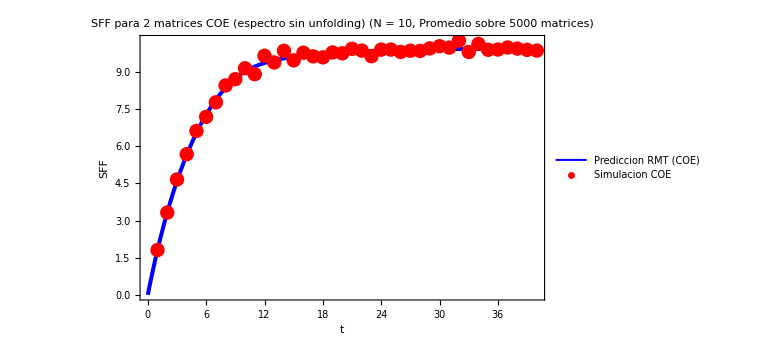

```mathematica
(*Calcular SFF para todas las matrices y todos los tiempos.sffAll sera una tabla 2D:{numMatrices,tMax}*)
sffAll=Table[sffInstance[phaseSets[[k]],t],{k,1,numMatrices},(*Loop sobre las matrices*){t,tValues}          (*Loop sobre el tiempo*)];

(*Promediar sobre todas las realizaciones de matrices (la primera dimension) para obtener el SFF simulado final.*)
sffSimulated=Mean[sffAll];

(*Combinar with tValues para graficar*)
simulatedData=Transpose[{tValues,sffSimulated/k}];
(*simulatedData=Transpose[{tValues,Around@@@Transpose[{Mean[sffAll],StandardDeviation[sffAll]/Sqrt[n]}]}];*)

(***4. Graficacion***)

ListPlot[{Table[{t,rmtSFF[t,n]},{t,0,tMax,0.1}],simulatedData},
(*Estilo de la grafica*)
PlotRange->{All,{Automatic,Automatic}},
Joined->{True,False},
PlotMarkers->{None,Automatic},
PlotStyle->{
{Blue,Thickness[0.005]}, (*Prediccion RMT*)
{Red,PointSize[0.018]} (*Datos de simulacion*)
},
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t","SFF"},

(*Etiquetas y Leyendas*)
PlotLegends->Placed[LineLegend[{"Prediccion RMT (COE)","Simulacion COE"},LegendMarkerSize->25],{Right,Bottom}],
LabelStyle->Directive[Black,FontSize->25],
AxesLabel->{"Tiempo t (entero)","Factor de Forma Espectral K(t)"},PlotLabel->Style["SFF para "<>ToString[k]<>" matrices COE (espectro sin unfolding)\n(N = "<>ToString[n]<>", Promedio sobre "<>ToString[numMatrices]<>" matrices)",Black,FontSize->25],ImageSize->Large]
```

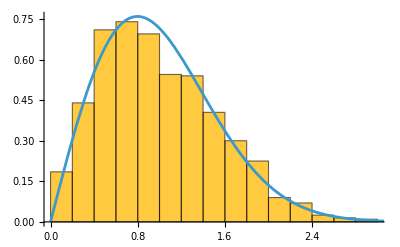

```mathematica
(*Generar dos matrices del COE*)
o=Table[RandomVariate[CircularOrthogonalMatrixDistribution[1000]],1];

(*Obtener los argumentos (fases) de sus eigenvalores*)
ephases=Flatten[Arg[Eigenvalues[#]]&/@o];

(*Unfold the eigenphases*)
ephasesUnfolded=#/Mean[Differences[#]]&[Sort[ephases]];

(*Graficar la P(s)*)
Show[
Histogram[Differences[ephasesUnfolded],Automatic,"PDF"],
Plot[PDF[RayleighDistribution[Sqrt[2/Pi]],s],{s,0,4}]
]
```

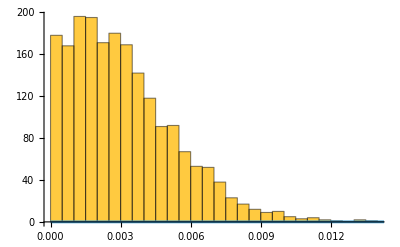

```mathematica
(*Generar dos matrices del COE*)
o=Table[RandomVariate[CircularOrthogonalMatrixDistribution[1000]],2];

(*Obtener los argumentos (fases) de sus eigenvalores*)
ephases=Flatten[Arg[Eigenvalues[#]]&/@o];

(*Unfold the eigenphases*)
(*ephasesUnfolded=#/Mean[Differences[#]]&[Sort[ephases]];*)

(*Graficar la P(s)*)
Show[
Histogram[Differences[Sort[ephases]],Automatic,"PDF"],
Plot[PDF[RayleighDistribution[Sqrt[2/Pi]],s],{s,0,4}]
]
```

```mathematica
(*Generar dos matrices del COE*)
o=Table[RandomVariate[CircularOrthogonalMatrixDistribution[1000]],2];

(*Obtener los argumentos (fases) de sus eigenvalores*)
ephases=Flatten[Arg[Eigenvalues[#]]&/@o];

(*Unfold the eigenphases*)
ephasesUnfolded=#/Mean[Differences[#]]&[Sort[ephases]];
```

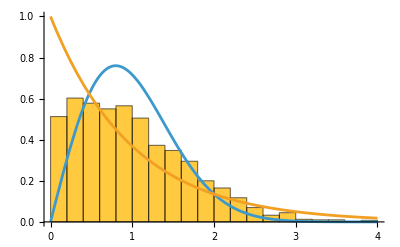

```mathematica
(*Graficar la P(s)*)
Show[
Histogram[Differences[ephasesUnfolded],Automatic,"PDF"],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],Exp[-s]},{s,0,4}]
]
```

```mathematica
(*Generar dos matrices del COE*)
o=Table[RandomVariate[CircularOrthogonalMatrixDistribution[2000]],2];

(*Obtener los argumentos (fases) de sus eigenvalores*)
ephases=Flatten[Arg[Eigenvalues[#]]&/@o];

(*Unfold the eigenphases*)
ephasesUnfolded=#/Mean[Differences[#]]&[Sort[ephases]];
```

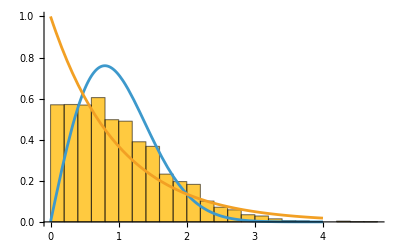

```mathematica
(*Graficar la P(s)*)
Show[
Histogram[Differences[ephasesUnfolded],Automatic,"PDF"],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],Exp[-s]},{s,0,4}]
]
```

```mathematica
(*Generar dos matrices del COE*)
o=Table[RandomVariate[CircularOrthogonalMatrixDistribution[3000]],2];

(*Obtener los argumentos (fases) de sus eigenvalores*)
ephases=Flatten[Arg[Eigenvalues[#]]&/@o];

(*Unfold the eigenphases*)
ephasesUnfolded=#/Mean[Differences[#]]&[Sort[ephases]];
```

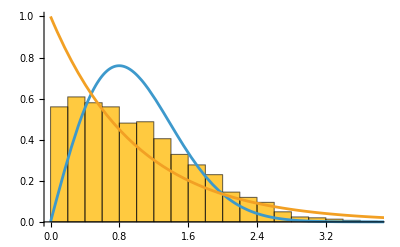

```mathematica
(*Graficar la P(s)*)
Show[
Histogram[Differences[ephasesUnfolded],Automatic,"PDF"],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],Exp[-s]},{s,0,4}]
]
```

```mathematica
(*Generar dos matrices del COE*)
o=Table[RandomVariate[CircularOrthogonalMatrixDistribution[5000]],2];

(*Obtener los argumentos (fases) de sus eigenvalores*)
ephases=Flatten[Arg[Eigenvalues[#]]&/@o];

(*Unfold the eigenphases*)
ephasesUnfolded=#/Mean[Differences[#]]&[Sort[ephases]];
```

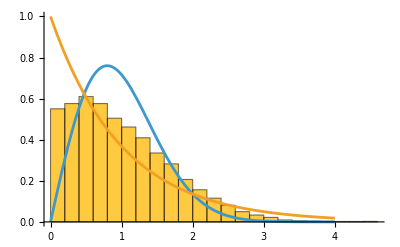

```mathematica
(*Graficar la P(s)*)
Show[
Histogram[Differences[ephasesUnfolded],Automatic,"PDF"],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],Exp[-s]},{s,0,4}]
]
```

```mathematica
n=L=8;
J=3.;U=1.;
evals=Eigenvalues[Normal@BoseHubbardHamiltonian[n,L,J,U,SymmetricSubspace->"EvenParity"]];
```

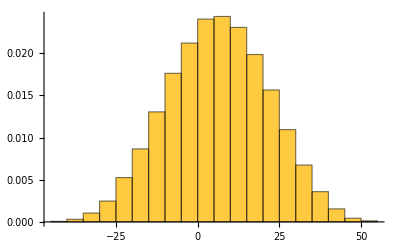

```mathematica
Histogram[evals,Automatic,"PDF"]
```

```mathematica
(*Función:AnalyzeDOSGaussian Descripción:Ajusta una función Gaussiana al histograma de una lista de eigenvalores.Input:-evals:Lista de eigenvalores numéricos.-nBins (Opcional):Número de bins para el histograma ("Automatic" por defecto).Output:Association con parámetros ajustados,bondad de ajuste y gráfico.*)AnalyzeDOSGaussian[evals_List,nBins:_:"Automatic"]:=
Module[
{
(*Variables locales*)
histoData,binEdges,binCounts,binCenters,dataXY,muGuess,sigmaGuess,ampGuess,nlm,params,fitFunction,plot},

(*1. Procesamiento de Datos:Usamos HistogramList para obtener datos crudos del histograma*)
{binEdges,binCounts}=HistogramList[evals];

(*Calculamos los centros de los bins de forma vectorizada*)
binCenters=MovingAverage[binEdges,2];

(*Creamos pares ordenados {energía,cuentas}*)
dataXY=Transpose[{binCenters,binCounts}];

(*2. Estimación Inicial Inteligente:Calculamos momentos estadísticos de los datos crudos para dar valores iniciales al fit y evitar divergencias.*)
muGuess=Mean[evals];
sigmaGuess=StandardDeviation[evals];
ampGuess=Max[binCounts];(*Altura aproximada*)

Print["hola"];

(*3. Ajuste No Lineal:Ajustamos A*Exp[-(x-mu)^2/(2*sigma^2)].Usamos MaxIterations para robustez en distribuciones ruidosas.*)nlm=NonlinearModelFit[dataXY,amp*Exp[-(x-mu)^2/(2 sigma^2)],{{amp,ampGuess},{mu,muGuess},{sigma,sigmaGuess}},x,MaxIterations->1000];

Print["hola"];
(*4. Extracción de Resultados*)
params=nlm["BestFitParameters"];Print[params];
fitFunction=nlm[x];Print[fitFunction];

(*5. Visualización Profesional*)plot=Show[Histogram[evals,Automatic,"Count",PlotLabel->"Densidad de Estados (DOS)"],Plot[fitFunction,{x,Min[evals],Max[evals]},PlotStyle->{Red,Thickness[0.005]},PlotRange->All],Frame->True,FrameLabel->{"Energía (E)","Conteo / DOS"},GridLines->Automatic,ImageSize->Medium];

(*6. Retorno Estructurado (Association)*)
Association["Model"->nlm,"Parameters"->params,
(*Regresa reglas mu->val,sigma->val*)
"Amplitude"->(amp/. params),"Mean"->(mu/. params),"Sigma"->(sigma/. params),"RSquared"->nlm["RSquared"],(*Coeficiente de determinación*)
"Plot"->plot]
]
```

hola

hola

{amp→402.07,mu→6.33415,sigma→16.2556}

402.07 ⅇ^(-0.00189219 (-6.33415+x)^2)

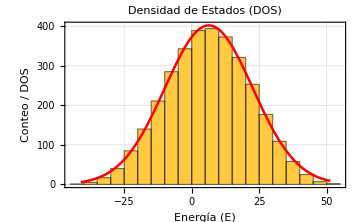

```mathematica
AnalyzeDOSGaussian[evals]["Plot"]
```

```mathematica
AnalyzeDOSGaussian[evals]["Mean"]
```

hola

hola

{amp→402.07,mu→6.33415,sigma→16.2556}

402.07 ⅇ^(-0.00189219 (-6.33415+x)^2)

6.33415

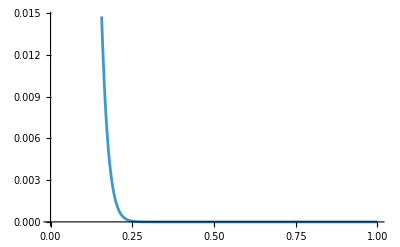

```mathematica
Plot[Exp[-6.3341480929779195*t-16.255580145503718^2/2*t^2],{t,0,1}]
```

```mathematica
N@MovingAverage[HistogramList[evals][[1]],2]
```

{-42.5,-37.5,-32.5,-27.5,-22.5,-17.5,-12.5,-7.5,-2.5,2.5,7.5,12.5,17.5,22.5,27.5,32.5,37.5,42.5,47.5,52.5}

## 2 COES con unfolding

```mathematica
ClearAll["Global`*"];

(*Codigo de Mathematica para simular el Factor de Forma Espectral (SFF) para el Ensamblaje Circular Ortogonal (COE)*)

(***1. Parametros***)

(*Cantidad de matrices*)
k=2;

(*Dimension de la matriz (N)*)
n=10;

(*Numero de matrices aleatorias para promediar*)
numMatrices=5000;

(*Tiempo maximo (entero) para calcular el SFF*)
(*Iremos a 4*n para ver tanto la rampa como el plateau*)
tMax=4*n;

(***2. Prediccion Teorica de RMT (para COE)***)

Print["Construyendo la prediccion teorica de RMT (COE)..."];

(*Prediccion de RMT para el SFF K(t)=<|Tr(O^t)|^2>para COE (beta=1) Para 1<=t<n,K(t)=2t-1 (la "rampa") Para t>=n,K(t)=2n-1 (el "plateau")*)
rmtSFF[τ_,n_Integer]:=With[{t=τ/n},n*If[t<1,2*t-t*Log[1+2*t],2-t*Log[(2*t+1)/(2*t-1)]]]

(*Crear una lista de pares {t,K(t)} para graficar*)
tValues=Range[1,tMax];
rmtData=Table[{t,rmtSFF[t,n]},{t,tValues}];


(***3. Simulacion Numerica de COE***)

Print["Iniciando simulacion de COE para "<>ToString[numMatrices]<>" matrices de dimension N="<>ToString[n]<>"..."];

(*Necesitamos las autofases {\\[Theta]_j} para cada matriz.Tr(O^t)=Sum[Exp[I*\\[Theta]_j*t]]*)

(*Generar todos los conjuntos de autofases primero*)
(*Este es el paso computacionalmente mas intensivo*)
phaseSets=
Table[
(*Generar k matrices COE*)
o=Table[RandomVariate[CircularOrthogonalMatrixDistribution[n]],k];

(*Obtener los argumentos (fases) de sus eigenvalores*)
#/Mean[Differences[Sort[#]]]&[Flatten[Arg[Eigenvalues[#]]&/@o]]

,{numMatrices}];

(*Funcion auxiliar para calcular SFF|Tr(O^t)|^2 para una*sola*matriz*)
sffInstance[phases_List,t_Integer]:=Abs[Total[Exp[I*phases*t]]]^2
```

Construyendo la prediccion teorica de RMT (COE)...

Iniciando simulacion de COE para 5000 matrices de dimension N=10...

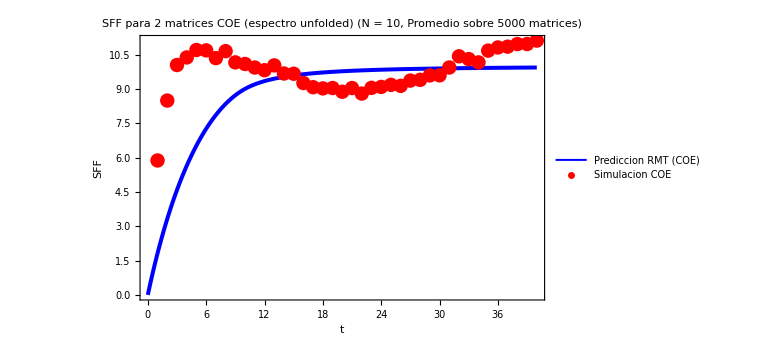

```mathematica
(*Calcular SFF para todas las matrices y todos los tiempos.sffAll sera una tabla 2D:{numMatrices,tMax}*)
sffAll=Table[sffInstance[phaseSets[[k]],t],{k,1,numMatrices},(*Loop sobre las matrices*){t,tValues}          (*Loop sobre el tiempo*)];

(*Promediar sobre todas las realizaciones de matrices (la primera dimension) para obtener el SFF simulado final.*)
sffSimulated=Mean[sffAll];

(*Combinar with tValues para graficar*)
simulatedData=Transpose[{tValues,sffSimulated/k}];
(*simulatedData=Transpose[{tValues,Around@@@Transpose[{Mean[sffAll],StandardDeviation[sffAll]/Sqrt[n]}]}];*)

(***4. Graficacion***)

ListPlot[{Table[{t,rmtSFF[t,n]},{t,0,tMax,0.1}],simulatedData},
(*Estilo de la grafica*)
PlotRange->{All,{Automatic,Automatic}},
Joined->{True,False},
PlotMarkers->{None,Automatic},
PlotStyle->{
{Blue,Thickness[0.005]}, (*Prediccion RMT*)
{Red,PointSize[0.018]} (*Datos de simulacion*)
},
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t","SFF"},

(*Etiquetas y Leyendas*)
PlotLegends->Placed[LineLegend[{"Prediccion RMT (COE)","Simulacion COE"},LegendMarkerSize->25],{Right,Bottom}],
LabelStyle->Directive[Black,FontSize->25],
AxesLabel->{"Tiempo t (entero)","Factor de Forma Espectral K(t)"},PlotLabel->Style["SFF para "<>ToString[k]<>" matrices COE (espectro unfolded)\n(N = "<>ToString[n]<>", Promedio sobre "<>ToString[numMatrices]<>" matrices)",Black,FontSize->25],ImageSize->Large]
```

## 2 COES con unfolding

```mathematica
(*Codigo de Mathematica para simular el Factor de Forma Espectral (SFF) para el Ensamblaje Circular Ortogonal (COE)*)

(***1. Parametros***)

(*Cantidad de matrices*)
k=10;

(*Dimension de la matriz (N)*)
n=10;

(*Numero de matrices aleatorias para promediar*)
numMatrices=5000;

(*Tiempo maximo (entero) para calcular el SFF*)
(*Iremos a 4*n para ver tanto la rampa como el plateau*)
tMax=4*n;

(***2. Prediccion Teorica de RMT (para COE)***)

Print["Construyendo la prediccion teorica de RMT (COE)..."];

(*Prediccion de RMT para el SFF K(t)=<|Tr(O^t)|^2>para COE (beta=1) Para 1<=t<n,K(t)=2t-1 (la "rampa") Para t>=n,K(t)=2n-1 (el "plateau")*)
rmtSFF[τ_,n_Integer]:=With[{t=τ/n},n*If[t<1,2*t-t*Log[1+2*t],2-t*Log[(2*t+1)/(2*t-1)]]]

(*Crear una lista de pares {t,K(t)} para graficar*)
tValues=Range[0.5,tMax,0.25];
rmtData=Table[{t,rmtSFF[t,n]},{t,tValues}];


(***3. Simulacion Numerica de COE***)

Print["Iniciando simulacion de COE para "<>ToString[numMatrices]<>" matrices de dimension N="<>ToString[n]<>"..."];

(*Necesitamos las autofases {\\[Theta]_j} para cada matriz.Tr(O^t)=Sum[Exp[I*\\[Theta]_j*t]]*)

(*Generar todos los conjuntos de autofases primero*)
(*Este es el paso computacionalmente mas intensivo*)
phaseSets=
Table[
(*Generar k matrices COE*)
o=Table[RandomVariate[GaussianOrthogonalMatrixDistribution[n]],k];

(*Obtener los argumentos (fases) de sus eigenvalores*)
(*#/Mean[Differences[Sort[#]]]&[Flatten[Arg[Eigenvalues[#]]&/@o]]*)
Flatten[Eigenvalues[#]&/@o]

,{numMatrices}];

(*Funcion auxiliar para calcular SFF|Tr(O^t)|^2 para una*sola*matriz*)
sffInstance[phases_List,t_]:=Abs[Total[Exp[I*phases*t]]]^2
```

Construyendo la prediccion teorica de RMT (COE)...

Iniciando simulacion de COE para 5000 matrices de dimension N=10...

```mathematica
(*Calcular SFF para todas las matrices y todos los tiempos.sffAll sera una tabla 2D:{numMatrices,tMax}*)
sffAll=Table[sffInstance[phaseSets[[k]],t],{k,1,numMatrices},(*Loop sobre las matrices*){t,tValues}          (*Loop sobre el tiempo*)];

(*Promediar sobre todas las realizaciones de matrices (la primera dimension) para obtener el SFF simulado final.*)
sffSimulated=Mean[sffAll];

(*Combinar with tValues para graficar*)
simulatedData10=Transpose[{tValues,sffSimulated/k}];
(*simulatedData=Transpose[{tValues,Around@@@Transpose[{Mean[sffAll],StandardDeviation[sffAll]/Sqrt[n]}]}];*)
```

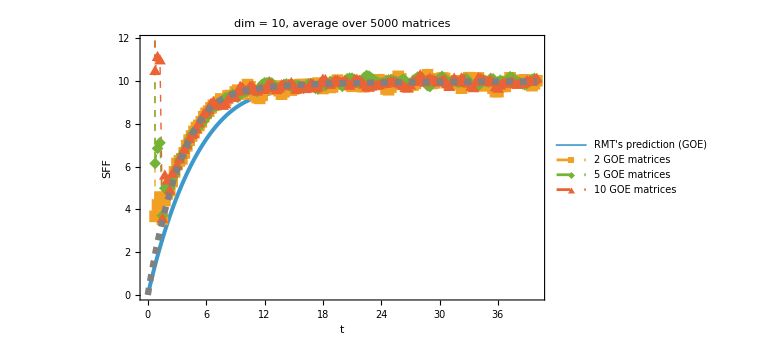

```mathematica
(***4. Graficacion***)

Show[
ListPlot[{Table[{t,rmtSFF[t,n]},{t,0,tMax,0.1}],simulatedData2,simulatedData5,simulatedData10},
(*Estilo de la grafica*)
PlotRange->{All,{Automatic,Automatic}},
Joined->{True,True},
PlotMarkers->{None,{Automatic,12},{Automatic,12},{Automatic,12}},
PlotStyle->{
{Thickness[0.005]}, (*Prediccion RMT*)
{Thin,Dashed}, (*Datos de simulacion*)
{Thin,Dashed},
{Thin,Dashed}
},
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t","SFF"},

(*Etiquetas y Leyendas*)
PlotLegends->Placed[LineLegend[{"RMT's prediction (GOE)","2 GOE matrices","5 GOE matrices","10 GOE matrices"},LegendMarkerSize->{30,15}],{Right,Bottom}],
LabelStyle->Directive[Black,FontSize->20],
AxesLabel->{"Tiempo t (entero)","Factor de Forma Espectral K(t)"},PlotLabel->Style["dim = "<>ToString[n]<>", average over "<>ToString[numMatrices]<>" matrices",Black,FontSize->25],ImageSize->Large],
Plot[With[{t=1.4*τ/n},n*If[t<1,2*t-t*Log[1+2*t],2-t*Log[(2*t+1)/(2*t-1)]]],{τ,0,40},PlotStyle->{Gray,Dashed,Thickness[0.008]},PlotRange->All]
]
```

```mathematica
With[{t=1.4*τ/n},n*If[t<1,2*t-t*Log[1+2*t],2-t*Log[(2*t+1)/(2*t-1)]]]/.τ->1.5
```

3.46362

```mathematica
simulatedData2
```

{{0.5,43.6136},{0.75,3.6716},{1.,4.20061},{1.25,4.57158},{1.5,3.53961},{1.75,4.40921},{2.,4.72521},{2.25,4.88145},{2.5,5.30001},{2.75,5.74936},{3.,6.13763},{3.25,6.2635},{3.5,6.35451},{3.75,6.63778},{4.,6.9715},{4.25,7.23179},{4.5,7.4282},{4.75,7.63778},{5.,7.81644},{5.25,7.92028},{5.5,8.08941},{5.75,8.32888},{6.,8.48542},{6.25,8.58698},{6.5,8.74264},{6.75,8.86312},{7.,8.88787},{7.25,9.0063},{7.5,9.15586},{7.75,9.09858},{8.,9.10443},{8.25,9.29635},{8.5,9.31737},{8.75,9.29209},{9.,9.48339},{9.25,9.56531},{9.5,9.39729},{9.75,9.40133},{10.,9.67682},{10.25,9.82665},{10.5,9.72806},{10.75,9.53537},{11.,9.34117},{11.25,9.2247},{11.5,9.18565},{11.75,9.32885},{12.,9.65174},{12.25,9.74175},{12.5,9.61453},{12.75,9.64869},{13.,9.76134},{13.25,9.73203},{13.5,9.54568},{13.75,9.38198},{14.,9.4934},{14.25,9.76387},{14.5,9.76396},{14.75,9.57054},{15.,9.6298},{15.25,9.78928},{15.5,9.81086},{15.75,9.82947},{16.,9.82386},{16.25,9.80019},{16.5,9.82806},{16.75,9.8267},{17.,9.80227},{17.25,9.85924},{17.5,9.89716},{17.75,9.75858},{18.,9.64887},{18.25,9.72603},{18.5,9.77417},{18.75,9.69588},{19.,9.72322},{19.25,9.94222},{19.5,10.0344},{19.75,9.92094},{20.,9.86794},{20.25,9.91185},{20.5,9.91807},{20.75,9.82509},{21.,9.75103},{21.25,9.84068},{21.5,9.97413},{21.75,9.91624},{22.,9.74107},{22.25,9.73635},{22.5,9.88585},{22.75,9.99516},{23.,9.97806},{23.25,9.90773},{23.5,9.96159},{23.75,10.0546},{24.,10.0092},{24.25,9.83576},{24.5,9.62764},{24.75,9.58854},{25.,9.71816},{25.25,9.85335},{25.5,10.0575},{25.75,10.2121},{26.,10.0984},{26.25,9.87313},{26.5,9.74605},{26.75,9.76682},{27.,9.81796},{27.25,9.80977},{27.5,9.88246},{27.75,10.0165},{28.,10.0355},{28.25,10.0257},{28.5,10.1758},{28.75,10.2876},{29.,10.0987},{29.25,9.88372},{29.5,9.91201},{29.75,10.0277},{30.,10.0917},{30.25,10.1313},{30.5,10.1181},{30.75,9.97275},{31.,9.83723},{31.25,9.87002},{31.5,9.96718},{31.75,10.0053},{32.,9.86978},{32.25,9.66249},{32.5,9.76352},{32.75,10.0712},{33.,10.1503},{33.25,10.0027},{33.5,9.91184},{33.75,10.0229},{34.,10.14},{34.25,9.99324},{34.5,9.77288},{34.75,9.80027},{35.,9.89248},{35.25,9.80983},{35.5,9.66212},{35.75,9.5036},{36.,9.50252},{36.25,9.74128},{36.5,9.79932},{36.75,9.7454},{37.,9.9751},{37.25,10.1458},{37.5,10.0217},{37.75,9.92268},{38.,9.938},{38.25,9.97361},{38.5,10.0224},{38.75,10.0487},{39.,9.9771},{39.25,9.83687},{39.5,9.77985},{39.75,9.8669},{40.,10.0081}}

```mathematica
simulatedData5
```

{{0.5,106.821},{0.75,6.14413},{1.,6.84659},{1.25,7.10947},{1.5,3.701},{1.75,4.98455},{2.,5.06846},{2.25,4.97001},{2.5,5.4129},{2.75,5.61068},{3.,5.9413},{3.25,6.30081},{3.5,6.53981},{3.75,6.72025},{4.,6.93145},{4.25,7.24524},{4.5,7.48535},{4.75,7.61995},{5.,7.75641},{5.25,7.86594},{5.5,7.97396},{5.75,8.12627},{6.,8.29328},{6.25,8.49682},{6.5,8.69803},{6.75,8.78171},{7.,8.81104},{7.25,8.88672},{7.5,8.98218},{7.75,9.11187},{8.,9.20995},{8.25,9.21853},{8.5,9.30288},{8.75,9.38233},{9.,9.27959},{9.25,9.23493},{9.5,9.39572},{9.75,9.51203},{10.,9.48832},{10.25,9.54243},{10.5,9.66436},{10.75,9.64872},{11.,9.54278},{11.25,9.49774},{11.5,9.62},{11.75,9.83919},{12.,9.91444},{12.25,9.91522},{12.5,9.95175},{12.75,9.90254},{13.,9.78378},{13.25,9.69103},{13.5,9.69615},{13.75,9.76294},{14.,9.8153},{14.25,9.86366},{14.5,9.82783},{14.75,9.7138},{15.,9.70675},{15.25,9.79027},{15.5,9.79306},{15.75,9.70741},{16.,9.65691},{16.25,9.7439},{16.5,9.86492},{16.75,9.86185},{17.,9.77122},{17.25,9.65135},{17.5,9.62256},{17.75,9.74969},{18.,9.80217},{18.25,9.7759},{18.5,9.87599},{18.75,9.96708},{19.,9.92987},{19.25,9.94468},{19.5,9.99407},{19.75,9.85612},{20.,9.74616},{20.25,9.92241},{20.5,10.1028},{20.75,10.1284},{21.,10.1298},{21.25,10.0697},{21.5,9.94225},{21.75,9.89472},{22.,9.99639},{22.25,10.1651},{22.5,10.255},{22.75,10.2215},{23.,10.1314},{23.25,10.0469},{23.5,9.97131},{23.75,9.91211},{24.,9.89628},{24.25,9.92108},{24.5,9.99354},{24.75,10.049},{25.,10.0373},{25.25,10.026},{25.5,9.98398},{25.75,9.93929},{26.,10.002},{26.25,10.0756},{26.5,10.0083},{26.75,9.86409},{27.,9.86795},{27.25,9.99088},{27.5,10.092},{27.75,10.1818},{28.,10.1964},{28.25,10.1135},{28.5,9.96464},{28.75,9.7824},{29.,9.73537},{29.25,9.88504},{29.5,9.99657},{29.75,10.0171},{30.,10.132},{30.25,10.2155},{30.5,10.1143},{30.75,9.98686},{31.,9.94389},{31.25,9.97032},{31.5,10.0079},{31.75,9.96222},{32.,9.91385},{32.25,9.97725},{32.5,10.0812},{32.75,10.117},{33.,9.97845},{33.25,9.79608},{33.5,9.81605},{33.75,9.84978},{34.,9.78113},{34.25,9.89368},{34.5,10.0631},{34.75,9.97841},{35.,9.94296},{35.25,10.1189},{35.5,10.0986},{35.75,9.9326},{36.,9.96278},{36.25,10.0291},{36.5,9.96571},{36.75,9.94347},{37.,10.0702},{37.25,10.196},{37.5,10.1538},{37.75,10.0336},{38.,9.97214},{38.25,9.93011},{38.5,9.86285},{38.75,9.83058},{39.,9.87027},{39.25,9.95519},{39.5,10.0787},{39.75,10.1196},{40.,10.013}}

```mathematica
simulatedData10
```

{{0.5,212.454},{0.75,10.5107},{1.,11.1672},{1.25,11.0075},{1.5,3.60601},{1.75,5.62693},{2.,5.39079},{2.25,4.93071},{2.5,5.70273},{2.75,5.8606},{3.,6.06393},{3.25,6.38535},{3.5,6.60691},{3.75,6.83197},{4.,7.04105},{4.25,7.33118},{4.5,7.51498},{4.75,7.55039},{5.,7.77751},{5.25,8.06446},{5.5,8.26596},{5.75,8.47598},{6.,8.57643},{6.25,8.70153},{6.5,8.98657},{6.75,9.05461},{7.,8.89237},{7.25,8.91073},{7.5,8.9618},{7.75,8.88309},{8.,8.95158},{8.25,9.17774},{8.5,9.3213},{8.75,9.27653},{9.,9.28081},{9.25,9.5477},{9.5,9.77517},{9.75,9.72133},{10.,9.58704},{10.25,9.61887},{10.5,9.78068},{10.75,9.79651},{11.,9.62583},{11.25,9.55211},{11.5,9.65055},{11.75,9.67874},{12.,9.62698},{12.25,9.75319},{12.5,9.93494},{12.75,9.87673},{13.,9.69544},{13.25,9.61703},{13.5,9.69619},{13.75,9.85212},{14.,9.87991},{14.25,9.79663},{14.5,9.85198},{14.75,9.95666},{15.,9.8241},{15.25,9.62852},{15.5,9.66574},{15.75,9.77825},{16.,9.75382},{16.25,9.6666},{16.5,9.72675},{16.75,9.92122},{17.,9.88908},{17.25,9.69555},{17.5,9.74673},{17.75,9.96192},{18.,10.1127},{18.25,10.095},{18.5,9.93934},{18.75,9.86346},{19.,9.95083},{19.25,10.065},{19.5,10.068},{19.75,9.97832},{20.,9.96878},{20.25,10.0483},{20.5,9.96514},{20.75,9.81946},{21.,9.91476},{21.25,10.0898},{21.5,10.1086},{21.75,10.0603},{22.,9.99574},{22.25,9.87302},{22.5,9.76189},{22.75,9.72815},{23.,9.77721},{23.25,9.83086},{23.5,9.82913},{23.75,9.84102},{24.,9.88832},{24.25,9.90602},{24.5,9.91449},{24.75,9.96928},{25.,10.0037},{25.25,9.9894},{25.5,9.96892},{25.75,9.93151},{26.,9.88247},{26.25,9.8132},{26.5,9.71239},{26.75,9.68849},{27.,9.8389},{27.25,10.0055},{27.5,10.0108},{27.75,10.1011},{28.,10.3158},{28.25,10.1891},{28.5,9.96988},{28.75,10.088},{29.,10.1614},{29.25,10.1},{29.5,10.0638},{29.75,9.9854},{30.,9.98312},{30.25,10.0716},{30.5,10.0755},{30.75,9.8895},{31.,9.76441},{31.25,9.9865},{31.5,10.16},{31.75,10.0285},{32.,10.0083},{32.25,10.1663},{32.5,10.1122},{32.75,9.95383},{33.,9.92481},{33.25,9.77735},{33.5,9.70795},{33.75,9.98784},{34.,10.1914},{34.25,10.1536},{34.5,10.0771},{34.75,10.0133},{35.,10.0146},{35.25,10.0683},{35.5,9.97638},{35.75,9.74913},{36.,9.68291},{36.25,9.8298},{36.5,9.9321},{36.75,9.9245},{37.,9.93912},{37.25,9.99287},{37.5,9.98952},{37.75,9.89177},{38.,9.86379},{38.25,9.91004},{38.5,9.90724},{38.75,9.96068},{39.,10.0474},{39.25,10.0286},{39.5,10.0045},{39.75,10.0854},{40.,10.1516}}

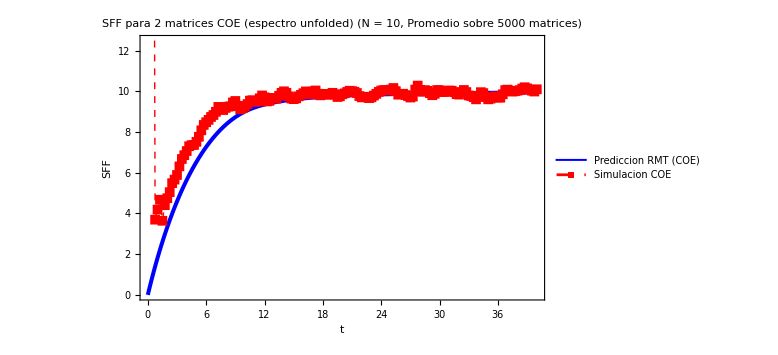
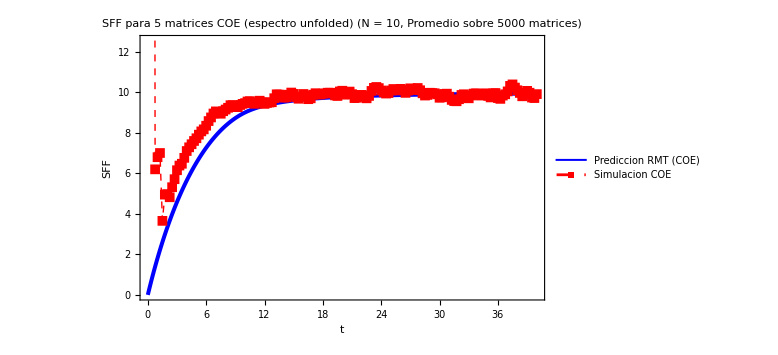
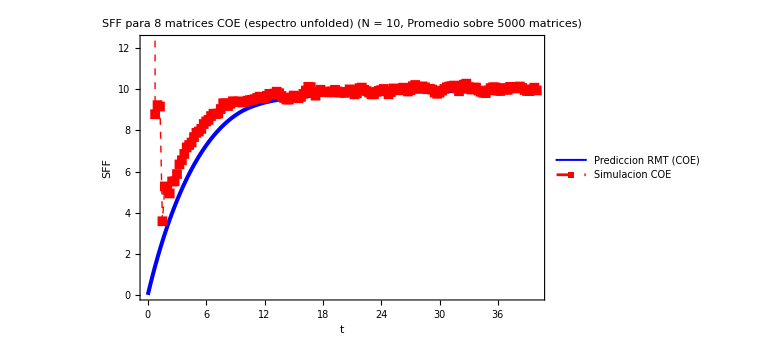

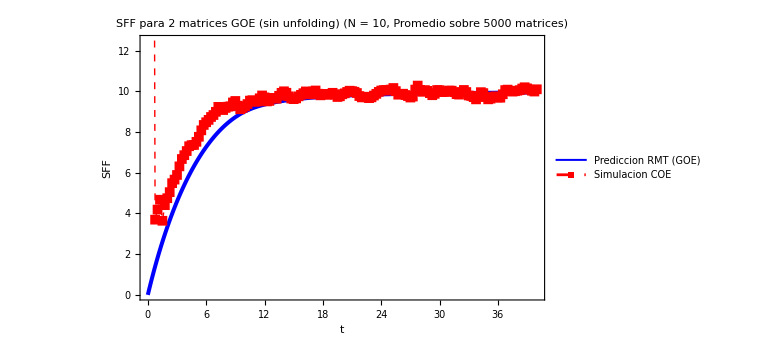

```mathematica
(***4. Graficacion***)

ListPlot[{Table[{t,rmtSFF[t,n]},{t,0,tMax,0.1}],simulatedData},
(*Estilo de la grafica*)
PlotRange->{All,{Automatic,Automatic}},
Joined->{True,True},
PlotMarkers->{None,{Automatic,10}},
PlotStyle->{
{Blue,Thickness[0.005]}, (*Prediccion RMT*)
{Thin,Dashed,Red} (*Datos de simulacion*)
},
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t","SFF"},

(*Etiquetas y Leyendas*)
PlotLegends->Placed[LineLegend[{"Prediccion RMT (GOE)","Simulacion COE"},LegendMarkerSize->25],{Right,Bottom}],
LabelStyle->Directive[Black,FontSize->25],
AxesLabel->{"Tiempo t (entero)","Factor de Forma Espectral K(t)"},PlotLabel->Style["SFF para "<>ToString[k]<>" matrices GOE (sin unfolding)\n(N = "<>ToString[n]<>", Promedio sobre "<>ToString[numMatrices]<>" matrices)",Black,FontSize->25],ImageSize->Large]
```

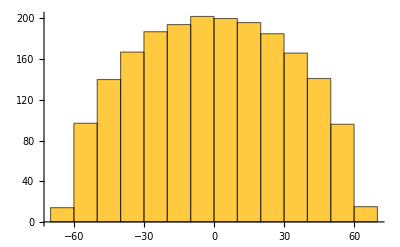

```mathematica
Histogram[Eigenvalues@RandomVariate[GaussianOrthogonalMatrixDistribution[2000]],Automatic,"Count"]
```

## 2 COES con unfolding

```mathematica
(*Codigo de Mathematica para simular el Factor de Forma Espectral (SFF) para el Ensamblaje Circular Ortogonal (COE)*)

(***1. Parametros***)

(*Cantidad de matrices*)
k=10;

(*Dimension de la matriz (N)*)
n=10;

(*Numero de matrices aleatorias para promediar*)
numMatrices=5000;

(*Tiempo maximo (entero) para calcular el SFF*)
(*Iremos a 4*n para ver tanto la rampa como el plateau*)
tMax=4*n;

(***2. Prediccion Teorica de RMT (para COE)***)

Print["Construyendo la prediccion teorica de RMT (COE)..."];

(*Prediccion de RMT para el SFF K(t)=<|Tr(O^t)|^2>para COE (beta=1) Para 1<=t<n,K(t)=2t-1 (la "rampa") Para t>=n,K(t)=2n-1 (el "plateau")*)
rmtSFF[τ_,n_Integer]:=With[{t=τ/n},n*If[t<1,2*t-t*Log[1+2*t],2-t*Log[(2*t+1)/(2*t-1)]]]

(*Crear una lista de pares {t,K(t)} para graficar*)
tValues=Range[0.5,tMax,0.25];
rmtData=Table[{t,rmtSFF[t,n]},{t,tValues}];


(***3. Simulacion Numerica de COE***)

Print["Iniciando simulacion de COE para "<>ToString[numMatrices]<>" matrices de dimension N="<>ToString[n]<>"..."];

(*Necesitamos las autofases {\\[Theta]_j} para cada matriz.Tr(O^t)=Sum[Exp[I*\\[Theta]_j*t]]*)

(*Generar todos los conjuntos de autofases primero*)
(*Este es el paso computacionalmente mas intensivo*)
phaseSets=
Table[
(*Generar k matrices COE*)
o=Table[RandomVariate[GaussianOrthogonalMatrixDistribution[n]],k];

(*Obtener los argumentos (fases) de sus eigenvalores*)
(*#/Mean[Differences[Sort[#]]]&[Flatten[Arg[Eigenvalues[#]]&/@o]]*)
Flatten[Eigenvalues[#]&/@o]

,{numMatrices}];

(*Funcion auxiliar para calcular SFF|Tr(O^t)|^2 para una*sola*matriz*)
sffInstance[phases_List,t_]:=Abs[Total[Exp[I*phases*t]]]^2
```

Construyendo la prediccion teorica de RMT (COE)...

Iniciando simulacion de COE para 5000 matrices de dimension N=10...

```mathematica
(*Calcular SFF para todas las matrices y todos los tiempos.sffAll sera una tabla 2D:{numMatrices,tMax}*)
sffAll=Table[sffInstance[phaseSets[[k]],t],{k,1,numMatrices},(*Loop sobre las matrices*){t,tValues}          (*Loop sobre el tiempo*)];

(*Promediar sobre todas las realizaciones de matrices (la primera dimension) para obtener el SFF simulado final.*)
sffSimulated=Mean[sffAll];

(*Combinar with tValues para graficar*)
simulatedData10=Transpose[{tValues,sffSimulated/k}];
(*simulatedData=Transpose[{tValues,Around@@@Transpose[{Mean[sffAll],StandardDeviation[sffAll]/Sqrt[n]}]}];*)
```

```mathematica
(***4. Graficacion***)

Show[
ListPlot[{Table[{t,rmtSFF[t,n]},{t,0,tMax,0.1}],simulatedData2,simulatedData5,simulatedData10},
(*Estilo de la grafica*)
PlotRange->{All,{Automatic,Automatic}},
Joined->{True,True},
PlotMarkers->{None,{Automatic,12},{Automatic,12},{Automatic,12}},
PlotStyle->{
{Thickness[0.005]}, (*Prediccion RMT*)
{Thin,Dashed}, (*Datos de simulacion*)
{Thin,Dashed},
{Thin,Dashed}
},
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t","SFF"},

(*Etiquetas y Leyendas*)
PlotLegends->Placed[LineLegend[{"RMT's prediction (GOE)","2 GOE matrices","5 GOE matrices","10 GOE matrices"},LegendMarkerSize->{30,15}],{Right,Bottom}],
LabelStyle->Directive[Black,FontSize->20],
AxesLabel->{"Tiempo t (entero)","Factor de Forma Espectral K(t)"},PlotLabel->Style["dim = "<>ToString[n]<>", average over "<>ToString[numMatrices]<>" matrices",Black,FontSize->25],ImageSize->Large],
Plot[With[{t=1.4*τ/n},n*If[t<1,2*t-t*Log[1+2*t],2-t*Log[(2*t+1)/(2*t-1)]]],{τ,0,40},PlotStyle->{Gray,Dashed,Thickness[0.008]},PlotRange->All]
]
```

-Graphics-

```mathematica
With[{t=1.4*τ/n},n*If[t<1,2*t-t*Log[1+2*t],2-t*Log[(2*t+1)/(2*t-1)]]]/.τ->1.5
```

3.46362

```mathematica
simulatedData2
```

{{0.5,43.6136},{0.75,3.6716},{1.,4.20061},{1.25,4.57158},{1.5,3.53961},{1.75,4.40921},{2.,4.72521},{2.25,4.88145},{2.5,5.30001},{2.75,5.74936},{3.,6.13763},{3.25,6.2635},{3.5,6.35451},{3.75,6.63778},{4.,6.9715},{4.25,7.23179},{4.5,7.4282},{4.75,7.63778},{5.,7.81644},{5.25,7.92028},{5.5,8.08941},{5.75,8.32888},{6.,8.48542},{6.25,8.58698},{6.5,8.74264},{6.75,8.86312},{7.,8.88787},{7.25,9.0063},{7.5,9.15586},{7.75,9.09858},{8.,9.10443},{8.25,9.29635},{8.5,9.31737},{8.75,9.29209},{9.,9.48339},{9.25,9.56531},{9.5,9.39729},{9.75,9.40133},{10.,9.67682},{10.25,9.82665},{10.5,9.72806},{10.75,9.53537},{11.,9.34117},{11.25,9.2247},{11.5,9.18565},{11.75,9.32885},{12.,9.65174},{12.25,9.74175},{12.5,9.61453},{12.75,9.64869},{13.,9.76134},{13.25,9.73203},{13.5,9.54568},{13.75,9.38198},{14.,9.4934},{14.25,9.76387},{14.5,9.76396},{14.75,9.57054},{15.,9.6298},{15.25,9.78928},{15.5,9.81086},{15.75,9.82947},{16.,9.82386},{16.25,9.80019},{16.5,9.82806},{16.75,9.8267},{17.,9.80227},{17.25,9.85924},{17.5,9.89716},{17.75,9.75858},{18.,9.64887},{18.25,9.72603},{18.5,9.77417},{18.75,9.69588},{19.,9.72322},{19.25,9.94222},{19.5,10.0344},{19.75,9.92094},{20.,9.86794},{20.25,9.91185},{20.5,9.91807},{20.75,9.82509},{21.,9.75103},{21.25,9.84068},{21.5,9.97413},{21.75,9.91624},{22.,9.74107},{22.25,9.73635},{22.5,9.88585},{22.75,9.99516},{23.,9.97806},{23.25,9.90773},{23.5,9.96159},{23.75,10.0546},{24.,10.0092},{24.25,9.83576},{24.5,9.62764},{24.75,9.58854},{25.,9.71816},{25.25,9.85335},{25.5,10.0575},{25.75,10.2121},{26.,10.0984},{26.25,9.87313},{26.5,9.74605},{26.75,9.76682},{27.,9.81796},{27.25,9.80977},{27.5,9.88246},{27.75,10.0165},{28.,10.0355},{28.25,10.0257},{28.5,10.1758},{28.75,10.2876},{29.,10.0987},{29.25,9.88372},{29.5,9.91201},{29.75,10.0277},{30.,10.0917},{30.25,10.1313},{30.5,10.1181},{30.75,9.97275},{31.,9.83723},{31.25,9.87002},{31.5,9.96718},{31.75,10.0053},{32.,9.86978},{32.25,9.66249},{32.5,9.76352},{32.75,10.0712},{33.,10.1503},{33.25,10.0027},{33.5,9.91184},{33.75,10.0229},{34.,10.14},{34.25,9.99324},{34.5,9.77288},{34.75,9.80027},{35.,9.89248},{35.25,9.80983},{35.5,9.66212},{35.75,9.5036},{36.,9.50252},{36.25,9.74128},{36.5,9.79932},{36.75,9.7454},{37.,9.9751},{37.25,10.1458},{37.5,10.0217},{37.75,9.92268},{38.,9.938},{38.25,9.97361},{38.5,10.0224},{38.75,10.0487},{39.,9.9771},{39.25,9.83687},{39.5,9.77985},{39.75,9.8669},{40.,10.0081}}

```mathematica
simulatedData5
```

{{0.5,106.821},{0.75,6.14413},{1.,6.84659},{1.25,7.10947},{1.5,3.701},{1.75,4.98455},{2.,5.06846},{2.25,4.97001},{2.5,5.4129},{2.75,5.61068},{3.,5.9413},{3.25,6.30081},{3.5,6.53981},{3.75,6.72025},{4.,6.93145},{4.25,7.24524},{4.5,7.48535},{4.75,7.61995},{5.,7.75641},{5.25,7.86594},{5.5,7.97396},{5.75,8.12627},{6.,8.29328},{6.25,8.49682},{6.5,8.69803},{6.75,8.78171},{7.,8.81104},{7.25,8.88672},{7.5,8.98218},{7.75,9.11187},{8.,9.20995},{8.25,9.21853},{8.5,9.30288},{8.75,9.38233},{9.,9.27959},{9.25,9.23493},{9.5,9.39572},{9.75,9.51203},{10.,9.48832},{10.25,9.54243},{10.5,9.66436},{10.75,9.64872},{11.,9.54278},{11.25,9.49774},{11.5,9.62},{11.75,9.83919},{12.,9.91444},{12.25,9.91522},{12.5,9.95175},{12.75,9.90254},{13.,9.78378},{13.25,9.69103},{13.5,9.69615},{13.75,9.76294},{14.,9.8153},{14.25,9.86366},{14.5,9.82783},{14.75,9.7138},{15.,9.70675},{15.25,9.79027},{15.5,9.79306},{15.75,9.70741},{16.,9.65691},{16.25,9.7439},{16.5,9.86492},{16.75,9.86185},{17.,9.77122},{17.25,9.65135},{17.5,9.62256},{17.75,9.74969},{18.,9.80217},{18.25,9.7759},{18.5,9.87599},{18.75,9.96708},{19.,9.92987},{19.25,9.94468},{19.5,9.99407},{19.75,9.85612},{20.,9.74616},{20.25,9.92241},{20.5,10.1028},{20.75,10.1284},{21.,10.1298},{21.25,10.0697},{21.5,9.94225},{21.75,9.89472},{22.,9.99639},{22.25,10.1651},{22.5,10.255},{22.75,10.2215},{23.,10.1314},{23.25,10.0469},{23.5,9.97131},{23.75,9.91211},{24.,9.89628},{24.25,9.92108},{24.5,9.99354},{24.75,10.049},{25.,10.0373},{25.25,10.026},{25.5,9.98398},{25.75,9.93929},{26.,10.002},{26.25,10.0756},{26.5,10.0083},{26.75,9.86409},{27.,9.86795},{27.25,9.99088},{27.5,10.092},{27.75,10.1818},{28.,10.1964},{28.25,10.1135},{28.5,9.96464},{28.75,9.7824},{29.,9.73537},{29.25,9.88504},{29.5,9.99657},{29.75,10.0171},{30.,10.132},{30.25,10.2155},{30.5,10.1143},{30.75,9.98686},{31.,9.94389},{31.25,9.97032},{31.5,10.0079},{31.75,9.96222},{32.,9.91385},{32.25,9.97725},{32.5,10.0812},{32.75,10.117},{33.,9.97845},{33.25,9.79608},{33.5,9.81605},{33.75,9.84978},{34.,9.78113},{34.25,9.89368},{34.5,10.0631},{34.75,9.97841},{35.,9.94296},{35.25,10.1189},{35.5,10.0986},{35.75,9.9326},{36.,9.96278},{36.25,10.0291},{36.5,9.96571},{36.75,9.94347},{37.,10.0702},{37.25,10.196},{37.5,10.1538},{37.75,10.0336},{38.,9.97214},{38.25,9.93011},{38.5,9.86285},{38.75,9.83058},{39.,9.87027},{39.25,9.95519},{39.5,10.0787},{39.75,10.1196},{40.,10.013}}

```mathematica
simulatedData10
```

{{0.5,212.454},{0.75,10.5107},{1.,11.1672},{1.25,11.0075},{1.5,3.60601},{1.75,5.62693},{2.,5.39079},{2.25,4.93071},{2.5,5.70273},{2.75,5.8606},{3.,6.06393},{3.25,6.38535},{3.5,6.60691},{3.75,6.83197},{4.,7.04105},{4.25,7.33118},{4.5,7.51498},{4.75,7.55039},{5.,7.77751},{5.25,8.06446},{5.5,8.26596},{5.75,8.47598},{6.,8.57643},{6.25,8.70153},{6.5,8.98657},{6.75,9.05461},{7.,8.89237},{7.25,8.91073},{7.5,8.9618},{7.75,8.88309},{8.,8.95158},{8.25,9.17774},{8.5,9.3213},{8.75,9.27653},{9.,9.28081},{9.25,9.5477},{9.5,9.77517},{9.75,9.72133},{10.,9.58704},{10.25,9.61887},{10.5,9.78068},{10.75,9.79651},{11.,9.62583},{11.25,9.55211},{11.5,9.65055},{11.75,9.67874},{12.,9.62698},{12.25,9.75319},{12.5,9.93494},{12.75,9.87673},{13.,9.69544},{13.25,9.61703},{13.5,9.69619},{13.75,9.85212},{14.,9.87991},{14.25,9.79663},{14.5,9.85198},{14.75,9.95666},{15.,9.8241},{15.25,9.62852},{15.5,9.66574},{15.75,9.77825},{16.,9.75382},{16.25,9.6666},{16.5,9.72675},{16.75,9.92122},{17.,9.88908},{17.25,9.69555},{17.5,9.74673},{17.75,9.96192},{18.,10.1127},{18.25,10.095},{18.5,9.93934},{18.75,9.86346},{19.,9.95083},{19.25,10.065},{19.5,10.068},{19.75,9.97832},{20.,9.96878},{20.25,10.0483},{20.5,9.96514},{20.75,9.81946},{21.,9.91476},{21.25,10.0898},{21.5,10.1086},{21.75,10.0603},{22.,9.99574},{22.25,9.87302},{22.5,9.76189},{22.75,9.72815},{23.,9.77721},{23.25,9.83086},{23.5,9.82913},{23.75,9.84102},{24.,9.88832},{24.25,9.90602},{24.5,9.91449},{24.75,9.96928},{25.,10.0037},{25.25,9.9894},{25.5,9.96892},{25.75,9.93151},{26.,9.88247},{26.25,9.8132},{26.5,9.71239},{26.75,9.68849},{27.,9.8389},{27.25,10.0055},{27.5,10.0108},{27.75,10.1011},{28.,10.3158},{28.25,10.1891},{28.5,9.96988},{28.75,10.088},{29.,10.1614},{29.25,10.1},{29.5,10.0638},{29.75,9.9854},{30.,9.98312},{30.25,10.0716},{30.5,10.0755},{30.75,9.8895},{31.,9.76441},{31.25,9.9865},{31.5,10.16},{31.75,10.0285},{32.,10.0083},{32.25,10.1663},{32.5,10.1122},{32.75,9.95383},{33.,9.92481},{33.25,9.77735},{33.5,9.70795},{33.75,9.98784},{34.,10.1914},{34.25,10.1536},{34.5,10.0771},{34.75,10.0133},{35.,10.0146},{35.25,10.0683},{35.5,9.97638},{35.75,9.74913},{36.,9.68291},{36.25,9.8298},{36.5,9.9321},{36.75,9.9245},{37.,9.93912},{37.25,9.99287},{37.5,9.98952},{37.75,9.89177},{38.,9.86379},{38.25,9.91004},{38.5,9.90724},{38.75,9.96068},{39.,10.0474},{39.25,10.0286},{39.5,10.0045},{39.75,10.0854},{40.,10.1516}}

```mathematica
(***4. Graficacion***)

ListPlot[{Table[{t,rmtSFF[t,n]},{t,0,tMax,0.1}],simulatedData},
(*Estilo de la grafica*)
PlotRange->{All,{Automatic,Automatic}},
Joined->{True,True},
PlotMarkers->{None,{Automatic,10}},
PlotStyle->{
{Blue,Thickness[0.005]}, (*Prediccion RMT*)
{Thin,Dashed,Red} (*Datos de simulacion*)
},
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t","SFF"},

(*Etiquetas y Leyendas*)
PlotLegends->Placed[LineLegend[{"Prediccion RMT (GOE)","Simulacion COE"},LegendMarkerSize->25],{Right,Bottom}],
LabelStyle->Directive[Black,FontSize->25],
AxesLabel->{"Tiempo t (entero)","Factor de Forma Espectral K(t)"},PlotLabel->Style["SFF para "<>ToString[k]<>" matrices GOE (sin unfolding)\n(N = "<>ToString[n]<>", Promedio sobre "<>ToString[numMatrices]<>" matrices)",Black,FontSize->25],ImageSize->Large]
```

-Graphics-

```mathematica
Histogram[Eigenvalues@RandomVariate[GaussianOrthogonalMatrixDistribution[2000]],Automatic,"Count"]
```

-Graphics-

## 2 COES con unfolding

```mathematica
(*Codigo de Mathematica para simular el Factor de Forma Espectral (SFF) para el Ensamblaje Circular Ortogonal (COE)*)

(***1. Parametros***)

(*Cantidad de matrices*)
k=10;

(*Dimension de la matriz (N)*)
n=10;

(*Numero de matrices aleatorias para promediar*)
numMatrices=5000;

(*Tiempo maximo (entero) para calcular el SFF*)
(*Iremos a 4*n para ver tanto la rampa como el plateau*)
tMax=4*n;

(***2. Prediccion Teorica de RMT (para COE)***)

Print["Construyendo la prediccion teorica de RMT (COE)..."];

(*Prediccion de RMT para el SFF K(t)=<|Tr(O^t)|^2>para COE (beta=1) Para 1<=t<n,K(t)=2t-1 (la "rampa") Para t>=n,K(t)=2n-1 (el "plateau")*)
rmtSFF[τ_,n_Integer]:=With[{t=τ/n},n*If[t<1,2*t-t*Log[1+2*t],2-t*Log[(2*t+1)/(2*t-1)]]]

(*Crear una lista de pares {t,K(t)} para graficar*)
tValues=Range[0.5,tMax,0.25];
rmtData=Table[{t,rmtSFF[t,n]},{t,tValues}];


(***3. Simulacion Numerica de COE***)

Print["Iniciando simulacion de COE para "<>ToString[numMatrices]<>" matrices de dimension N="<>ToString[n]<>"..."];

(*Necesitamos las autofases {\\[Theta]_j} para cada matriz.Tr(O^t)=Sum[Exp[I*\\[Theta]_j*t]]*)

(*Generar todos los conjuntos de autofases primero*)
(*Este es el paso computacionalmente mas intensivo*)
phaseSets=
Table[
(*Generar k matrices COE*)
o=Table[RandomVariate[GaussianOrthogonalMatrixDistribution[n]],k];

(*Obtener los argumentos (fases) de sus eigenvalores*)
(*#/Mean[Differences[Sort[#]]]&[Flatten[Arg[Eigenvalues[#]]&/@o]]*)
Unfold[Flatten[Eigenvalues[#]&/@o]]["UnfoldedLevels"]

,{numMatrices}];

(*Funcion auxiliar para calcular SFF|Tr(O^t)|^2 para una*sola*matriz*)
sffInstance[phases_List,t_]:=Abs[Total[Exp[I*phases*t]]]^2
```

Construyendo la prediccion teorica de RMT (COE)...

Iniciando simulacion de COE para 5000 matrices de dimension N=10...

```mathematica
(*Calcular SFF para todas las matrices y todos los tiempos.sffAll sera una tabla 2D:{numMatrices,tMax}*)
sffAll=Table[sffInstance[phaseSets[[k]],t],{k,1,numMatrices},(*Loop sobre las matrices*){t,tValues}          (*Loop sobre el tiempo*)];

(*Promediar sobre todas las realizaciones de matrices (la primera dimension) para obtener el SFF simulado final.*)
sffSimulated=Mean[sffAll];

(*Combinar with tValues para graficar*)
simulatedData=Transpose[{tValues,sffSimulated/k}];
(*simulatedData=Transpose[{tValues,Around@@@Transpose[{Mean[sffAll],StandardDeviation[sffAll]/Sqrt[n]}]}];*)
```

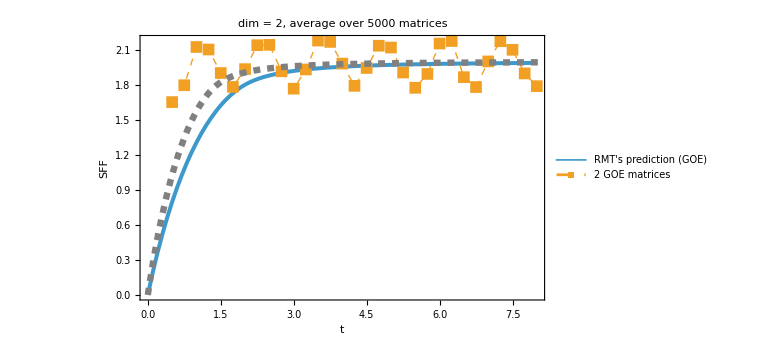

```mathematica
(***4. Graficacion***)

Show[
ListPlot[{Table[{t,rmtSFF[t,n]},{t,0,tMax,0.1}],simulatedData},
(*Estilo de la grafica*)
PlotRange->{All,{Automatic,Automatic}},
Joined->{True,True},
PlotMarkers->{None,{Automatic,12},{Automatic,12},{Automatic,12}},
PlotStyle->{
{Thickness[0.005]}, (*Prediccion RMT*)
{Thin,Dashed}, (*Datos de simulacion*)
{Thin,Dashed},
{Thin,Dashed}
},
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t","SFF"},

(*Etiquetas y Leyendas*)
PlotLegends->Placed[LineLegend[{"RMT's prediction (GOE)","2 GOE matrices","5 GOE matrices","10 GOE matrices"},LegendMarkerSize->{30,15}],{Right,Bottom}],
LabelStyle->Directive[Black,FontSize->20],
AxesLabel->{"Tiempo t (entero)","Factor de Forma Espectral K(t)"},PlotLabel->Style["dim = "<>ToString[n]<>", average over "<>ToString[numMatrices]<>" matrices",Black,FontSize->25],ImageSize->Large],
Plot[With[{t=1.4*τ/n},n*If[t<1,2*t-t*Log[1+2*t],2-t*Log[(2*t+1)/(2*t-1)]]],{τ,0,40},PlotStyle->{Gray,Dashed,Thickness[0.008]},PlotRange->All]
]
```

```mathematica
With[{t=1.4*τ/n},n*If[t<1,2*t-t*Log[1+2*t],2-t*Log[(2*t+1)/(2*t-1)]]]/.τ->1.5
```

3.46362

```mathematica
simulatedData2
```

{{0.5,43.6136},{0.75,3.6716},{1.,4.20061},{1.25,4.57158},{1.5,3.53961},{1.75,4.40921},{2.,4.72521},{2.25,4.88145},{2.5,5.30001},{2.75,5.74936},{3.,6.13763},{3.25,6.2635},{3.5,6.35451},{3.75,6.63778},{4.,6.9715},{4.25,7.23179},{4.5,7.4282},{4.75,7.63778},{5.,7.81644},{5.25,7.92028},{5.5,8.08941},{5.75,8.32888},{6.,8.48542},{6.25,8.58698},{6.5,8.74264},{6.75,8.86312},{7.,8.88787},{7.25,9.0063},{7.5,9.15586},{7.75,9.09858},{8.,9.10443},{8.25,9.29635},{8.5,9.31737},{8.75,9.29209},{9.,9.48339},{9.25,9.56531},{9.5,9.39729},{9.75,9.40133},{10.,9.67682},{10.25,9.82665},{10.5,9.72806},{10.75,9.53537},{11.,9.34117},{11.25,9.2247},{11.5,9.18565},{11.75,9.32885},{12.,9.65174},{12.25,9.74175},{12.5,9.61453},{12.75,9.64869},{13.,9.76134},{13.25,9.73203},{13.5,9.54568},{13.75,9.38198},{14.,9.4934},{14.25,9.76387},{14.5,9.76396},{14.75,9.57054},{15.,9.6298},{15.25,9.78928},{15.5,9.81086},{15.75,9.82947},{16.,9.82386},{16.25,9.80019},{16.5,9.82806},{16.75,9.8267},{17.,9.80227},{17.25,9.85924},{17.5,9.89716},{17.75,9.75858},{18.,9.64887},{18.25,9.72603},{18.5,9.77417},{18.75,9.69588},{19.,9.72322},{19.25,9.94222},{19.5,10.0344},{19.75,9.92094},{20.,9.86794},{20.25,9.91185},{20.5,9.91807},{20.75,9.82509},{21.,9.75103},{21.25,9.84068},{21.5,9.97413},{21.75,9.91624},{22.,9.74107},{22.25,9.73635},{22.5,9.88585},{22.75,9.99516},{23.,9.97806},{23.25,9.90773},{23.5,9.96159},{23.75,10.0546},{24.,10.0092},{24.25,9.83576},{24.5,9.62764},{24.75,9.58854},{25.,9.71816},{25.25,9.85335},{25.5,10.0575},{25.75,10.2121},{26.,10.0984},{26.25,9.87313},{26.5,9.74605},{26.75,9.76682},{27.,9.81796},{27.25,9.80977},{27.5,9.88246},{27.75,10.0165},{28.,10.0355},{28.25,10.0257},{28.5,10.1758},{28.75,10.2876},{29.,10.0987},{29.25,9.88372},{29.5,9.91201},{29.75,10.0277},{30.,10.0917},{30.25,10.1313},{30.5,10.1181},{30.75,9.97275},{31.,9.83723},{31.25,9.87002},{31.5,9.96718},{31.75,10.0053},{32.,9.86978},{32.25,9.66249},{32.5,9.76352},{32.75,10.0712},{33.,10.1503},{33.25,10.0027},{33.5,9.91184},{33.75,10.0229},{34.,10.14},{34.25,9.99324},{34.5,9.77288},{34.75,9.80027},{35.,9.89248},{35.25,9.80983},{35.5,9.66212},{35.75,9.5036},{36.,9.50252},{36.25,9.74128},{36.5,9.79932},{36.75,9.7454},{37.,9.9751},{37.25,10.1458},{37.5,10.0217},{37.75,9.92268},{38.,9.938},{38.25,9.97361},{38.5,10.0224},{38.75,10.0487},{39.,9.9771},{39.25,9.83687},{39.5,9.77985},{39.75,9.8669},{40.,10.0081}}

```mathematica
simulatedData5
```

{{0.5,106.821},{0.75,6.14413},{1.,6.84659},{1.25,7.10947},{1.5,3.701},{1.75,4.98455},{2.,5.06846},{2.25,4.97001},{2.5,5.4129},{2.75,5.61068},{3.,5.9413},{3.25,6.30081},{3.5,6.53981},{3.75,6.72025},{4.,6.93145},{4.25,7.24524},{4.5,7.48535},{4.75,7.61995},{5.,7.75641},{5.25,7.86594},{5.5,7.97396},{5.75,8.12627},{6.,8.29328},{6.25,8.49682},{6.5,8.69803},{6.75,8.78171},{7.,8.81104},{7.25,8.88672},{7.5,8.98218},{7.75,9.11187},{8.,9.20995},{8.25,9.21853},{8.5,9.30288},{8.75,9.38233},{9.,9.27959},{9.25,9.23493},{9.5,9.39572},{9.75,9.51203},{10.,9.48832},{10.25,9.54243},{10.5,9.66436},{10.75,9.64872},{11.,9.54278},{11.25,9.49774},{11.5,9.62},{11.75,9.83919},{12.,9.91444},{12.25,9.91522},{12.5,9.95175},{12.75,9.90254},{13.,9.78378},{13.25,9.69103},{13.5,9.69615},{13.75,9.76294},{14.,9.8153},{14.25,9.86366},{14.5,9.82783},{14.75,9.7138},{15.,9.70675},{15.25,9.79027},{15.5,9.79306},{15.75,9.70741},{16.,9.65691},{16.25,9.7439},{16.5,9.86492},{16.75,9.86185},{17.,9.77122},{17.25,9.65135},{17.5,9.62256},{17.75,9.74969},{18.,9.80217},{18.25,9.7759},{18.5,9.87599},{18.75,9.96708},{19.,9.92987},{19.25,9.94468},{19.5,9.99407},{19.75,9.85612},{20.,9.74616},{20.25,9.92241},{20.5,10.1028},{20.75,10.1284},{21.,10.1298},{21.25,10.0697},{21.5,9.94225},{21.75,9.89472},{22.,9.99639},{22.25,10.1651},{22.5,10.255},{22.75,10.2215},{23.,10.1314},{23.25,10.0469},{23.5,9.97131},{23.75,9.91211},{24.,9.89628},{24.25,9.92108},{24.5,9.99354},{24.75,10.049},{25.,10.0373},{25.25,10.026},{25.5,9.98398},{25.75,9.93929},{26.,10.002},{26.25,10.0756},{26.5,10.0083},{26.75,9.86409},{27.,9.86795},{27.25,9.99088},{27.5,10.092},{27.75,10.1818},{28.,10.1964},{28.25,10.1135},{28.5,9.96464},{28.75,9.7824},{29.,9.73537},{29.25,9.88504},{29.5,9.99657},{29.75,10.0171},{30.,10.132},{30.25,10.2155},{30.5,10.1143},{30.75,9.98686},{31.,9.94389},{31.25,9.97032},{31.5,10.0079},{31.75,9.96222},{32.,9.91385},{32.25,9.97725},{32.5,10.0812},{32.75,10.117},{33.,9.97845},{33.25,9.79608},{33.5,9.81605},{33.75,9.84978},{34.,9.78113},{34.25,9.89368},{34.5,10.0631},{34.75,9.97841},{35.,9.94296},{35.25,10.1189},{35.5,10.0986},{35.75,9.9326},{36.,9.96278},{36.25,10.0291},{36.5,9.96571},{36.75,9.94347},{37.,10.0702},{37.25,10.196},{37.5,10.1538},{37.75,10.0336},{38.,9.97214},{38.25,9.93011},{38.5,9.86285},{38.75,9.83058},{39.,9.87027},{39.25,9.95519},{39.5,10.0787},{39.75,10.1196},{40.,10.013}}

```mathematica
simulatedData10
```

{{0.5,212.454},{0.75,10.5107},{1.,11.1672},{1.25,11.0075},{1.5,3.60601},{1.75,5.62693},{2.,5.39079},{2.25,4.93071},{2.5,5.70273},{2.75,5.8606},{3.,6.06393},{3.25,6.38535},{3.5,6.60691},{3.75,6.83197},{4.,7.04105},{4.25,7.33118},{4.5,7.51498},{4.75,7.55039},{5.,7.77751},{5.25,8.06446},{5.5,8.26596},{5.75,8.47598},{6.,8.57643},{6.25,8.70153},{6.5,8.98657},{6.75,9.05461},{7.,8.89237},{7.25,8.91073},{7.5,8.9618},{7.75,8.88309},{8.,8.95158},{8.25,9.17774},{8.5,9.3213},{8.75,9.27653},{9.,9.28081},{9.25,9.5477},{9.5,9.77517},{9.75,9.72133},{10.,9.58704},{10.25,9.61887},{10.5,9.78068},{10.75,9.79651},{11.,9.62583},{11.25,9.55211},{11.5,9.65055},{11.75,9.67874},{12.,9.62698},{12.25,9.75319},{12.5,9.93494},{12.75,9.87673},{13.,9.69544},{13.25,9.61703},{13.5,9.69619},{13.75,9.85212},{14.,9.87991},{14.25,9.79663},{14.5,9.85198},{14.75,9.95666},{15.,9.8241},{15.25,9.62852},{15.5,9.66574},{15.75,9.77825},{16.,9.75382},{16.25,9.6666},{16.5,9.72675},{16.75,9.92122},{17.,9.88908},{17.25,9.69555},{17.5,9.74673},{17.75,9.96192},{18.,10.1127},{18.25,10.095},{18.5,9.93934},{18.75,9.86346},{19.,9.95083},{19.25,10.065},{19.5,10.068},{19.75,9.97832},{20.,9.96878},{20.25,10.0483},{20.5,9.96514},{20.75,9.81946},{21.,9.91476},{21.25,10.0898},{21.5,10.1086},{21.75,10.0603},{22.,9.99574},{22.25,9.87302},{22.5,9.76189},{22.75,9.72815},{23.,9.77721},{23.25,9.83086},{23.5,9.82913},{23.75,9.84102},{24.,9.88832},{24.25,9.90602},{24.5,9.91449},{24.75,9.96928},{25.,10.0037},{25.25,9.9894},{25.5,9.96892},{25.75,9.93151},{26.,9.88247},{26.25,9.8132},{26.5,9.71239},{26.75,9.68849},{27.,9.8389},{27.25,10.0055},{27.5,10.0108},{27.75,10.1011},{28.,10.3158},{28.25,10.1891},{28.5,9.96988},{28.75,10.088},{29.,10.1614},{29.25,10.1},{29.5,10.0638},{29.75,9.9854},{30.,9.98312},{30.25,10.0716},{30.5,10.0755},{30.75,9.8895},{31.,9.76441},{31.25,9.9865},{31.5,10.16},{31.75,10.0285},{32.,10.0083},{32.25,10.1663},{32.5,10.1122},{32.75,9.95383},{33.,9.92481},{33.25,9.77735},{33.5,9.70795},{33.75,9.98784},{34.,10.1914},{34.25,10.1536},{34.5,10.0771},{34.75,10.0133},{35.,10.0146},{35.25,10.0683},{35.5,9.97638},{35.75,9.74913},{36.,9.68291},{36.25,9.8298},{36.5,9.9321},{36.75,9.9245},{37.,9.93912},{37.25,9.99287},{37.5,9.98952},{37.75,9.89177},{38.,9.86379},{38.25,9.91004},{38.5,9.90724},{38.75,9.96068},{39.,10.0474},{39.25,10.0286},{39.5,10.0045},{39.75,10.0854},{40.,10.1516}}

```mathematica
(***4. Graficacion***)

ListPlot[{Table[{t,rmtSFF[t,n]},{t,0,tMax,0.1}],simulatedData},
(*Estilo de la grafica*)
PlotRange->{All,{Automatic,Automatic}},
Joined->{True,True},
PlotMarkers->{None,{Automatic,10}},
PlotStyle->{
{Blue,Thickness[0.005]}, (*Prediccion RMT*)
{Thin,Dashed,Red} (*Datos de simulacion*)
},
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t","SFF"},

(*Etiquetas y Leyendas*)
PlotLegends->Placed[LineLegend[{"Prediccion RMT (GOE)","Simulacion COE"},LegendMarkerSize->25],{Right,Bottom}],
LabelStyle->Directive[Black,FontSize->25],
AxesLabel->{"Tiempo t (entero)","Factor de Forma Espectral K(t)"},PlotLabel->Style["SFF para "<>ToString[k]<>" matrices GOE (sin unfolding)\n(N = "<>ToString[n]<>", Promedio sobre "<>ToString[numMatrices]<>" matrices)",Black,FontSize->25],ImageSize->Large]
```

-Graphics-

```mathematica
Histogram[Eigenvalues@RandomVariate[GaussianOrthogonalMatrixDistribution[2000]],Automatic,"Count"]
```

-Graphics-